### Modularity

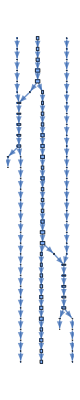
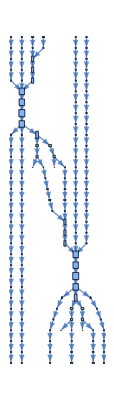
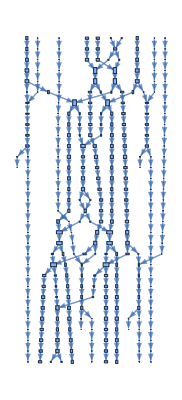
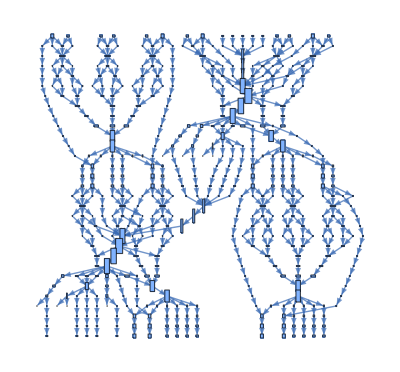
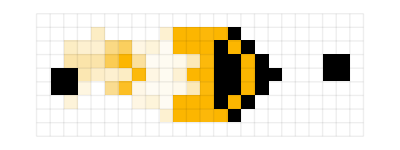
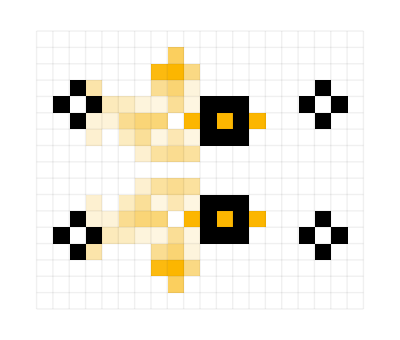
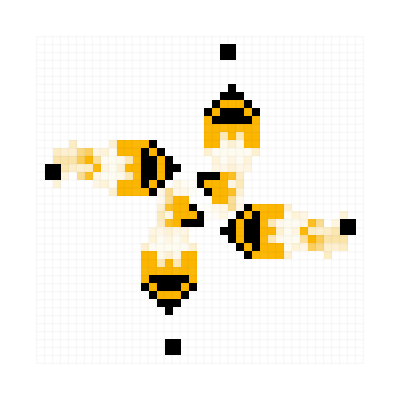
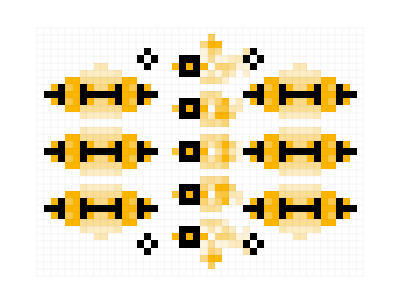
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics-1970
3.2 | -Graphics-1980
5.1 | -Graphics-1984
9.6 | -Graphics-1985
16.
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics-1995
2.8 | -Graphics-2022
9.5 | -Graphics-2022
3.1 | -Graphics-2022
11.

```mathematica
Grid[Catenate[Transpose/@Partition[Values[{GraphPlot[BoundingBoxLayeredGraph[#,Automatic], ImageSize->{Automatic, 200}],
Labeled[
Rotate[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},16,MeshStyle->Opacity[(.5/(Times@@Dimensions[#MatrixData])^.4)],ImageSize->12 Sqrt[Last[Dimensions[#MatrixData]]]], If[#Name === "p30rpentominohassler2", Pi/2, 0]],Column[{#Year,N[VertexCount[BoundingBoxLayeredGraph[#,#Period-1]]/#Period,2]}]]}&/@SortBy[Select[$LifeData,#Class==="Oscillator"&&#Period==30&]//Quiet,#Year&]], 4 ]], Frame->{All, {True, None, True, None, True}},FrameStyle->Opacity[.2], Alignment->Bottom]
```